# Delft’s Silicon device

reference: https://arxiv.org/abs/2202.09252
scientific contributors: Fernando, Simon

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
```

Load the QuESTLink

```mathematica
Import["https://qtechtheory.org/questlink.m"];
SetDirectory[NotebookDirectory[]];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Connectivity of this device

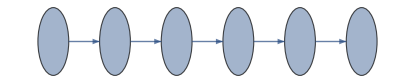

```mathematica
Graph[Range[0,5],Table[j->j+1,{j,0,4}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

Set the default configuration of the device

```mathematica
Options[SiliconDelft]={
qubitsNum->6,
(*average of T1*)
T1->100,
(* T2* *)
T2s-><|0->3,1-> 2.5,2-> 3.7,3-> 3.7,4-> 5.9,5-> 5.1|>,
(* T2 obtained by echo RX[π/2]-τ-RX[π]-τ-RX[π/2], where τ=1μs *)
T2-><|0->14,1-> 21.1,2-> 40.1,3-> 37.2,4-> 44.7,5-> 26.7|>,
(* Rabi frequency of each qubit in MHz *)
RabiFreq-><|0->15.62*10^3,1-> 15.88*10^3,2-> 16.3*10^3,3-> 16.1*10^3,4-> 15.9*10^3,5-> 15.69*10^3|>,
(* The electromagnetic field in Tesla *)
BField->0.576,
(* Fidelities of X- and Y- rotations by random benchmarking *)
FidSingleXY-><|0->0.9977,1-> 0.9987,2-> 0.9996,3-> 0.9988,4-> 0.9991,5-> 0.9989|>,
FreqSingleXY->5,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingleXY->{0,1},
(*  The rabi Frequency (MHz) and fidelities of controlled-Z, C[Z], nearest-neighbors, where the control qubits are the lower one. Keys are the control qubits *)
FreqCZ-><|0->12.1,1-> 11.1,2-> 6.6,3-> 9.8,4-> 5.4|>,
FidCZ-><|0->0.8961173996 ,1->0.903347176,2-> 0.8837068241 ,3->0.9582985365,4-> 0.9426960894|>,
(* Error fraction/ratio {depolarising, dephasing} *)
EFCZ->{0.2,0.8},
(* Crosstalks error (C-Rz[ex])on the passive qubits when applying CZ gates;square matrix with dims nqubit-2*)
ExchangeRotOn->{{0,0.023, 0.018 ,0.03, 0.04},{0.05 ,0,0.03, 0.03, 0.04},{0.05, 0.03 ,0,0.07, 0.042},{0.038 ,0.03 ,0.031,0 ,0.25},{0.033, 0.03 ,0.02, 0.03,0}
},
(* Crosstalks error (C-Rz[ex])on the passive qubits when no CZ gates applied *)
ExchangeRotOff-><|0->0.039,1-> 0.015 ,2->0.03 ,3->0.02,4-> 0.028|>,
(* average of Rabi frequency (MHz) and fidelities of Controlled-Rotations around x-axis. This gates are used in readout *)
FreqCRotX->5,
FidCRotX-><|0->0.9977,1-> 0.9987,2-> 0.9996,3-> 0.9988,4-> 0.9991|>,
(* Error fraction/ratio {depolarising, dephasing} for controlled-Rx  *)
EFCRotX->{0.5,0.5}
};
```

Native gates:
 Rx_j[θ],  Ry_j[θ],  Rz_j[θ],  C_i[Z_(i+1)], Wait_-1[Δt] 

C_i[Rx_j[θ]] (for measurement, conditional rotation)

## Test

Remarks:
the time unit is μs

```mathematica
dev=SiliconDelft[];
```

### Individual gate tests, complex passive noise

Single qubit gates: x- and y- rotations have the same error and z-rotations are virtual, instaneous

{{0,{Rx_0[2 π],Depol_0[0.],Deph_0[0.00345],U_1[{{0.870582+0.00818876 ⅈ,3.66376×10^-14-0.491955 ⅈ},{3.66376×10^-14-0.491955 ⅈ,0.870582-0.00818876 ⅈ}}],U_2[{{-0.798798+0.0261652 ⅈ,3.29691×10^-14-0.601031 ⅈ},{3.29691×10^-14-0.601031 ⅈ,-0.798798-0.0261652 ⅈ}}],U_3[{{-0.387265-0.0283186 ⅈ,5.28891×10^-12+0.921533 ⅈ},{5.28891×10^-12+0.921533 ⅈ,-0.387265+0.0283186 ⅈ}}],U_4[{{-0.0295314+0.017915 ⅈ,6.26744×10^-14-0.999403 ⅈ},{6.26744×10^-14-0.999403 ⅈ,-0.0295314-0.017915 ⅈ}}],U_5[{{0.881032+0.00211995 ⅈ,7.41649×10^-15-0.473052 ⅈ},{7.41649×10^-15-0.473052 ⅈ,0.881032-0.00211995 ⅈ}}]},{C_0[Rz_1[0.]],Deph_0[0.],Depol_0[0.],C_1[Rz_2[0.00095493]],Deph_1[0.0384418],Depol_1[0.0014985],C_2[Rz_3[0.00190986]],Deph_2[0.0263096],Depol_2[0.0014985],C_3[Rz_4[0.00127324]],Deph_3[0.0263096],Depol_3[0.0014985],C_4[Rz_5[0.00178254]],Deph_4[0.0166651],Depol_4[0.0014985],Deph_5[0.0192284],Depol_5[0.0014985]}},{1/5,{Rz_1[π]},{C_0[Rz_1[0.]],Deph_0[0.],Depol_0[0.],C_1[Rz_2[0.]],Deph_1[0.],Depol_1[0.],C_2[Rz_3[0.]],Deph_2[0.],Depol_2[0.],C_3[Rz_4[0.]],Deph_3[0.],Depol_3[0.],C_4[Rz_5[0.]],Deph_4[0.],Depol_4[0.],Deph_5[0.],Depol_5[0.]}},{1/5,{},{C_0[Rz_1[0.0124141]],Deph_0[0.141734],Depol_0[0.00746262],C_1[Rz_2[0.00477465]],Deph_1[0.16484],Depol_1[0.00746262],C_2[Rz_3[0.0095493]],Deph_2[0.118413],Depol_2[0.00746262],C_3[Rz_4[0.0063662]],Deph_3[0.118413],Depol_3[0.00746262],C_4[Rz_5[0.00891268]],Deph_4[0.077953],Depol_4[0.00746262],Deph_5[0.0890261],Depol_5[0.00746262]}},{6/5,{Ry_3[2 π],Depol_3[0.],Deph_3[0.0018],U_0[{{-0.885684+0.013836 ⅈ,-2.66349×10^-12+0.464083 ⅈ},{-2.66349×10^-12+0.464083 ⅈ,-0.885684-0.013836 ⅈ}}],U_1[{{0.00953594+0.0136627 ⅈ,-5.69924×10^-12+0.999861 ⅈ},{-5.69924×10^-12+0.999861 ⅈ,0.00953594-0.0136627 ⅈ}}],U_2[{{-0.724246-0.00856508 ⅈ,-3.99497×10^-12+0.689489 ⅈ},{-3.99497×10^-12+0.689489 ⅈ,-0.724246+0.00856508 ⅈ}}],U_4[{{-0.724246+0.00856508 ⅈ,-3.922×10^-12+0.689489 ⅈ},{-3.922×10^-12+0.689489 ⅈ,-0.724246-0.00856508 ⅈ}}],U_5[{{-0.771212+0.0162057 ⅈ,-3.55375×10^-12+0.636372 ⅈ},{-3.55375×10^-12+0.636372 ⅈ,-0.771212-0.0162057 ⅈ}}]},{C_0[Rz_1[0.00248282]],Deph_0[0.0322465],Depol_0[0.0014985],C_1[Rz_2[0.00095493]],Deph_1[0.0384418],Depol_1[0.0014985],C_2[Rz_3[0.00190986]],Deph_2[0.0263096],Depol_2[0.0014985],C_3[Rz_4[0.]],Deph_3[0.],Depol_3[0.],C_4[Rz_5[0.00178254]],Deph_4[0.0166651],Depol_4[0.0014985],Deph_5[0.0192284],Depol_5[0.0014985]}},{7/5,{Rz_0[2 π]},{C_0[Rz_1[0.]],Deph_0[0.],Depol_0[0.],C_1[Rz_2[0.]],Deph_1[0.],Depol_1[0.],C_2[Rz_3[0.]],Deph_2[0.],Depol_2[0.],C_3[Rz_4[0.]],Deph_3[0.],Depol_3[0.],C_4[Rz_5[0.]],Deph_4[0.],Depol_4[0.],Deph_5[0.],Depol_5[0.]}}}

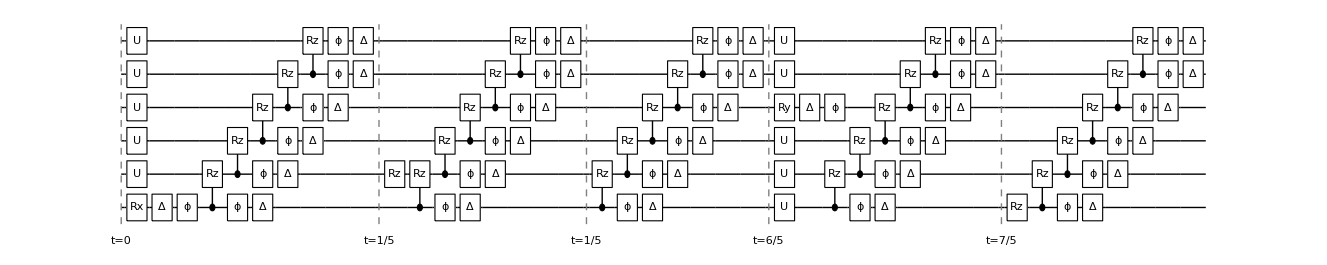

```mathematica
InsertCircuitNoise[{#}&/@{Subscript[Rx, 0][2π],Subscript[Rz, 1][π],Subscript[Wait, -1][1],Subscript[Ry, 3][2π],Subscript[Rz, 0][2π]},dev,ReplaceAliases->False]
DrawCircuit[%]
```

Two qubit gates: CZ is obtained by π Z-rotation. CZ gates comes with dephasing, depolarising, and crosstalk

```mathematica
Complement[{1,2,4,3},{3}]
```

{1,2,4}

```mathematica
OptionValue[SiliconDelft,ExchangeRotOff]
```

<|0→0.039,1→0.015,2→0.03,3→0.02,4→0.028|>

{{0,{C_0[Z_1],Depol_(0,1)[0.0265732],Deph_(0,1)[0.106293],C_1[Rz_2[0.023]],C_2[Rz_3[0.018]],C_3[Rz_4[0.03]],C_4[Rz_5[0.04]],C_2[Rz_3[-0.000394599]],C_3[Rz_4[-0.000263066]],C_4[Rz_5[-0.000368292]]},{C_0[Rz_1[0.]],Deph_0[0.],Depol_0[0.],C_1[Rz_2[0.]],Deph_1[0.],Depol_1[0.],C_2[Rz_3[0.000394599]],Deph_2[0.00555303],Depol_2[0.000309853],C_3[Rz_4[0.000263066]],Deph_3[0.00555303],Depol_3[0.000309853],C_4[Rz_5[0.000368292]],Deph_4[0.00348966],Depol_4[0.000309853],Deph_5[0.00403484],Depol_5[0.000309853]}},{0.0413223,{C_4[Z_5],Depol_(4,5)[0.0145055],Deph_(4,5)[0.0580221],C_0[Rz_1[0.033]],C_1[Rz_2[0.03]],C_2[Rz_3[0.02]],C_3[Rz_4[0.03]],C_0[Rz_1[-0.00114945]],C_1[Rz_2[-0.000442097]],C_2[Rz_3[-0.000884194]],C_3[Rz_4[-0.000589463]]},{C_0[Rz_1[0.00114945]],Deph_0[0.0151964],Depol_0[0.000694123],C_1[Rz_2[0.000442097]],Deph_1[0.0181798],Depol_1[0.000694123],C_2[Rz_3[0.000884194]],Deph_2[0.0123572],Depol_2[0.000694123],C_3[Rz_4[0.000589463]],Deph_3[0.0123572],Depol_3[0.000694123],C_4[Rz_5[0.]],Deph_4[0.],Depol_4[0.],Deph_5[0.],Depol_5[0.]}}}

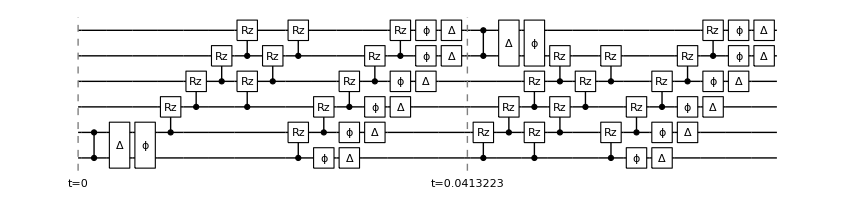

```mathematica
dev=SiliconDelft[];
InsertCircuitNoise[{{Subscript[C, 0][Subscript[Z, 1]]},{Subscript[C, 4][Subscript[Z, 5]]}},dev]
DrawCircuit[%]
```

## Reproducing results from the paper

Initialisation sequence
Measurement sequence
Obtain T2 epoch from the T2* 
Obtain Bell state preparation fidelity